# Fisher estimates for a power law mass spectrum

```mathematica
SetDirectory@NotebookDirectory[];
<<MaTeX`
```

## No selection effects

## Inputs

```mathematica
$Assumptions={θ>0,θmax>0,θmin>0,θmax>θmin, σ>0 & σ<1000,λ>-1}
```

{θ>0,θmax>0,θmin>0,θmax>θmin,σ (σ>0&)<1000,λ>-1}

```mathematica
pdetθ[M_]:=1
pdetλ[λ_]:=1
ppop[{θ_,θmax_,θmin_},λ_]:= λ/(θmax^λ-θmin^λ) θ^(λ-1)
```

```mathematica
Integrate[ppop[{θ,θmax,θmin},λ],{θ,θmin,θmax}] (* The population model is correctly normalized. *)
```

1

```mathematica
(*σ=1;*)
Γ = 1/σ^2;  (* True only in the case in which d = θ + noise. *)
Dmij= Γ ;  (* Only true in the absence of selection effects. *)
Dmi = D[pdetθ[θ],θ];
P = D[Log@ppop[{θ,θmin,θmax},λ],θ];
H = - D[D[Log@ppop[{θ,θmin,θmax},λ],θ],θ];
```

## Fisher matrix and precision estimates

Notice that M is integrated out in the interval 10^4 M_0< M < 10^7 M_0.

```mathematica
PopFisher[λ_,{θ_,θmax_,θmin_},{i_,j_}]:=
Integrate[(pdetθ[θ]/(ppop[{θ,θmin,θmax},λ]*pdetλ[λ]))D[ppop[{θ,θmin,θmax},λ],i]*D[ppop[{θ,θmin,θmax},λ],j],{θ,10^4,10^7}]- 1/pdetλ[λ]^2 D[pdetλ[λ],i]*D[pdetλ[λ],j] +1/2 Integrate[D[D[Log@(Γ+H),j],i] pdetθ[M]/pdetλ[λ] ppop[{θ,θmin,θmax},λ],{θ,10^4,10^7}]-1/2 Integrate[D[D[(Γ+H)^-1,j],i]Dmij ppop[{θ,θmin,θmax},λ]/pdetλ[λ],{θ,10^4,10^7}] - Integrate[D[D[P(Γ+H)^-1,j],i]Dmi ppop[{θ,θmin,θmax},λ]/pdetλ[λ],{θ,10^4,10^7}] -Integrate[D[D[P^2(Γ+H)^-1,j],i] ppop[{θ,θmin,θmax},λ]/pdetλ[λ],{θ,10^4,10^7}]
```

```mathematica
Γλλ = PopFisher[λ,{M,10^4,10^7},{λ,λ}];//Timing
```

{18.3718,Null}

```mathematica
Δα = √(1/(Nobs*Γλλ))
```

√(1/(Nobs (1/λ^2-(2 θ^4 σ^2)/((θ^2+(-1+λ) σ^2)^3)-(θ^2 σ^4)/((θ^2+(-1+λ) σ^2)^3)-σ^4/(2 (θ^2+(-1+λ) σ^2)^2)-(9 1000^λ Log[10]^2)/((-1+1000^λ)^2))))

```mathematica
λtrue = 0.00001;
truepars ={Nobs->1000,λ->λtrue,σ->0.1,θ->10^6,Mmax->10^7, Mmin->10^4}//N;
```

```mathematica
Δα/.truepars
```

0.0158814

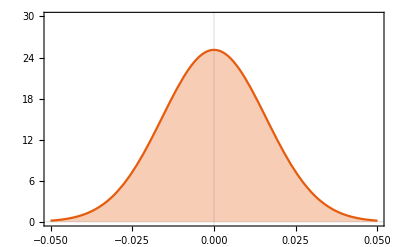

```mathematica
Plot[
PDF[NormalDistribution[λtrue,Δα/.truepars],x]//Evaluate,{x,-.05,.05},
Filling->Axis,PlotRange->{All,{0,30}},
FrameLabel->{{MaTeX["\\text{PDF}",FontSize->17],None},{MaTeX["\\alpha_0",FontSize->17],None}},
FrameTicksStyle->Directive[Black,13],
TicksStyle->Directive[Black,AbsoluteThickness[100]],
PlotTheme-> "Scientific", 
Frame->True]
```